# Assignment 1 - Valentina Greatti Pendolum with oscillating suspension point

Assignment 1:
1.For the period shift map of thependulum with oscillating suspension pointtreated in Section 3.5.A of the notes (and studied in the lab classes) plot,in the parameter space (α,k):
1.a the first few instability tongues of the lower fixed point z_=(0,0)
     1.b the stability region (regions?) of the upper fixed point z_+ =(π,0)

Suggestions:
Part 1.a  You should try to produce evidence
-of the existence of the tongues
-of the position of the tongues in the parameters plane (if there is an estimate on their position,your results do confirm it?)
-of the structure of the tongues(if there are theoretical informations available—even qualitative,such as cusp or angle—do your results demonstrate them?)
For 1.b,adapt the code and produce a picture in a meangiful region of the parameter space

THE MODEL:

Consider a pendolum with oscillating suspension point 2Pi-periodically as in the theory at Section 3.5.  After time rescaling the equation of motion is:      
     x’’=-(α^2 - k Cos[t]) Sin[x]     with initial conditions  x(0)=x0,  x’(0)=v0 ,
     where k=a/l <=2 .

In the phase space the equation of motion becomes a system of ODEs:
     x’=v
     v’=-(α^2 - k Cos[t]) Sin[x]            where (x,v) \in S^1 x R .
Points (0,0) and (Pi,0) are the equilibria.

But the suspension point oscillates 2Pi-periodically in time, due to the external force which is 2Pi-periodic, hence it results more convenient to work in the Quotient Extended Phase Space where the orbits traced by the equilibria are given by  t-->(0,0,t Mod .2Pi)  , t--->(Pi,0,t Mod .2Pi)  .
The equation of motion in the Quotient Extended Phase Space  S^1 x R x S^1 becomes: 
    x’=v
    v’=-(α^2 - k Cos[t]) Sin[x] 
    t’=1   mod 2Pi  .
    
From the theory orbits  correspond to fixed points of the Pointcaré Map ψ_(α,k) which is actually the Period Shift Map :  ψ_(α,k)= ϕ_(2π,0)  .
We need to linearize the Period Shift Map at fixed points, but from the theory its eigenvalues are those of the monodromy matrix without 1. And the monodromy matrix can be computed by solving the variational equation at time T=2Pi, with initial condition Id matrix.

I have computed aside the Variational Equation for both the orbits t-->(0,0,t)  and t-->(Pi,0,t)  of the equilibria, and  then integrated the VE equation in both cases with Runge Kutta 2, and done the analysis of the stability/instability regions in (α,k).

## Stability/Unstability regions for (0,0) fixed point:

SETUP :

```mathematica
XL[{a_,k_}][{x_,v_,t_}]:={v,-(a^2 - k Cos[t]) x , 1} ;          (*vector field of variational equation in extended phase space*)

RK2[ak_,h_][xvt_]:=xvt + h XL[ak][xvt+h/2 XL[ak][xvt]];            (*RK2 to approximate solutions of the variational equation*)

sol[ak_,n_,{x0_,v0_}]:=Take[Nest[RK2[ak,(2π)/n ],{x0,v0,0}, n],2];      
(*compute solution of variational equation, given initial data {x0,v0}, at time T=2π, n iterations*)
(*output just (x,v) first two entries*)

PSM[ak_,n_]:= {sol[ak,n,{1,0}] , sol[ak,n,{0,1}]};             (*Period Shift Map = Pointcaré Map, given initial conditions (1,0), (0,1)*)
```

USE COMPILE FOR SETUP, IN ORDER TO HAVE FASTER COMPUTATIONS  :

```mathematica
RK2[{a,k},h][{x,v,t}]
```

{x+h (v+1/2 h x (-a^2+k Cos[t])),v+h ((h v)/2+x) (-a^2+k Cos[h/2+t]),h+t}

```mathematica
RK2c= Compile[{{αk,_Real,1},{h,_Real},{xvt,_Real,1}},
{xvt[[1]]+h (xvt[[2]]+1/2 h xvt[[1]] (-αk[[1]]^2+αk[[2]] Cos[xvt[[3]]])),  
xvt[[2]]+h ((h xvt[[2]])/2+xvt[[1]]) (-αk[[1]]^2+αk[[2]] Cos[h/2+xvt[[3]]]),
   h+xvt[[3]]}] ;

(*RK2 already implemented with vector field XL inside, faster computations*)
```

```mathematica
solc=Compile[ {{αk,_Real,1},n,{xv,_Real,1}}, 
                                        Take[     Nest[RK2c[αk,(2π)/n,#]&,Append[xv,0],n]   , 2] ];

(* # & converts the slot # into a input for the function*)
```

```mathematica
PSMc[ak_,n_]:={solc[ak,n,{1,0}],solc[ak,n,{0,1}]} ;

(*Period shift map=Pointcaré Map*)
```

STUDY OF LYAPUNOV STABILITY WRTO (a,k) AND PLOT UNSTABLE POINTS :

We need to study the spectrum of the linearization of PSMc at (0,0), i.e Ψ_(α,k)'(0,0), made of 2 eigenvalues.
As noticed in the theory the dynamical system conserves the volume, hence the product of the two eigenvalues is 1, and by the Lyapunov Stability Criterium:
|Tr(Ψ_(α,k)'(0,0))| <= 2  if and only if (0,0) Lyapunov Stable ;
|Tr(Ψ_(α,k)'(0,0))| > 2  if and only if (0,0) Lyapunov Unstable .

We choose this derivation of the criterium because it doesn’t require to compute explicitely the eigenvalues of PSM, but it’s enough to compute its trace.
Then plot unstable points.

```mathematica
αkTr[ak_,n_]:={  ak,   Abs[Tr[ PSMc[ak,n]]   ]  }  ;           (* ((a,k),|Tr|) *)

RandαkTr[n_, a1_,a2_, k1_, k2_]:= αkTr[{RandomReal[{a1,a2}],RandomReal[{k1,k2}]}, n ] ;          (* ((a,k),|Tr|) with a,k random *)

critTr[eps_][lst_]:=  lst[[-1]]>2+eps   ;                                           (*criterion |trace| > 2 + eps *)

UnstTr[lst_,eps_]:=Select[lst,critTr[eps]] ;                              (* select those ((a,k),|Tr|) with |Tr| > 2 + eps , i.e. unstable *)

PlotUnstTr[lst_,eps_, a1_, a2_, k1_, k2_]:=ListPlot[  Transpose[UnstTr[lst,eps]][[1]] ,PlotRange->{{a1,a2},{k1,k2}} , AxesLabel->{"α","k"}  ]   ;

(*plot unstable points (α,k)*)
```

```mathematica
randpoints1 =  Table[RandαkTr[1000,0, 2, 0,2], 10000] ;      //Timing          (*increase number of  points and iterations, for more accuracy*)
```

{7.96875,Null}

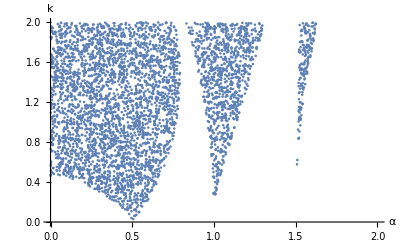

```mathematica
PlotUnstTr[randpoints1, 0.0001, 0, 2, 0, 2]
```

```mathematica
randpoints2 =  Table[RandαkTr[1000,0, 2, 0,2], 50000] ;        //Timing              (*increase number of points*)
```

{40.0469,Null}

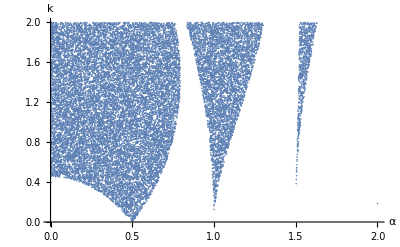

```mathematica
PlotUnstTr[randpoints2, 0.000001, 0, 2, 0, 2]                                  (*UNSTABILITY GLOBAL PORTRAIT*)
```

This plot represents a global portrait of the instability zones, i.e. for which points (α,k) the equilibrium (0,0) is Lyapunov unstable.
While the regions with no points are the stability zones. 

The instability regions are tongues (existence proved).

Notice that for k=0 , just for some specific α the equilibria is unstable, where the tongues intersect the horizontal axis . 
From the theory we know that this can happen only at  |Tr|=2  iff  α = n/2 , where n is any integer .
These points are those at stability boundary, where the system transitions from stability to instability regions and viceversa.

If k=0 , more likely (0,0) is stable, but we can force α ,which depends on the frequency of the external force, to make (0,0) unstable.

At  (k,α)=(0, n/2) for any positive integer n,  the instability tongues end with a cusp point. 
In the following I check numerically that at every multiple of 0.5 we have an instability tongue:

```mathematica
randpoints3 = Table[RandαkTr[1000,0.3, 0.7, 0.,0.2], 50000] ;    //Timing           (*(k,α)=(0, 1/2), n=1*)
```

{39.6875,Null}

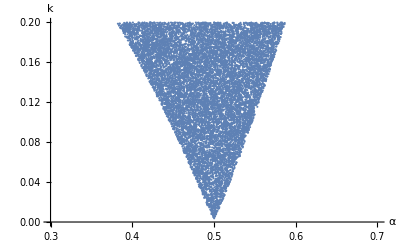

```mathematica
PlotUnstTr[randpoints3, 0.0001, 0.3, 0.7, 0., 0.2]
```

```mathematica
randpoints4 = Table[RandαkTr[1000,0.9, 1.1, 0.,0.2], 50000] ;    //Timing           (*(k,α)=(0, 2/2),n=2*)
```

{40.1563,Null}

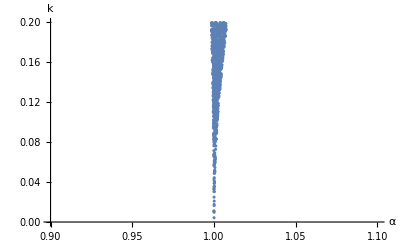

```mathematica
PlotUnstTr[randpoints4, 0.00000001, 0.9, 1.1, 0., 0.2]
```